```mathematica
f0=0.1234
```

0.1234

```mathematica
f0x=0.9876
```

0.9876

```mathematica
f1=0.5678
```

0.5678

```mathematica
f1x=-0.1111
```

-0.1111

```mathematica
f2=1
```

1

```mathematica
f2x=2
```

2

```mathematica
c0=f0
```

0.1234

```mathematica
c1=3*c0+f0x
```

1.3578

```mathematica
c3=f1
```

0.5678

```mathematica
c2=3*c3-f1x
```

1.8145

```mathematica
g=c0*(1-x)^3+c1*x*(1-x)^2+c2*x^2*(1-x)+c3*x^3
```

0.1234 (1-x)^3+1.3578 (1-x)^2 x+1.8145 (1-x) x^2+0.5678 x^3

```mathematica
gx=D[g,x]
```

0.9876 (1-x)^2+0.9134 (1-x) x-0.1111 x^2

```mathematica
d0=f1
```

0.5678

```mathematica
d1=3*d0+f1x
```

1.5923

```mathematica
d3=f2
```

1

```mathematica
d2=3*d3-f2x
```

1

```mathematica
h=d0*(2-x)^3+d1*(x-1)*(2-x)^2+d2*(x-1)^2*(2-x)+d3*(x-1)^3
```

0.5678 (2-x)^3+1.5923 (2-x)^2 (-1+x)+(2-x) (-1+x)^2+(-1+x)^3

```mathematica
hx=D[h,x]
```

-0.1111 (2-x)^2-1.1846 (2-x) (-1+x)+2 (-1+x)^2

```mathematica
p0=Plot[g,{x,0,1}];
```

```mathematica
p1=Plot[h,{x,1,2}];
```

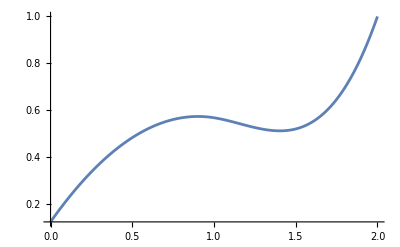

```mathematica
Show[p0,p1,PlotRange->All]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteCubic1Order0Multiple.txt","CSV"];
```

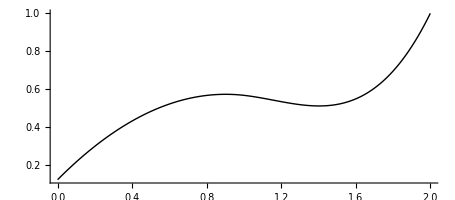

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```

```mathematica
p0=Plot[gx,{x,0,1}];
```

```mathematica
p1=Plot[hx,{x,1,2}];
```

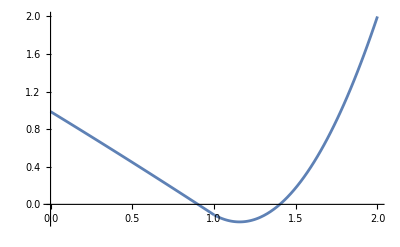

```mathematica
Show[p0,p1,PlotRange->All]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteCubic1OrderXMultiple.txt","CSV"];
```

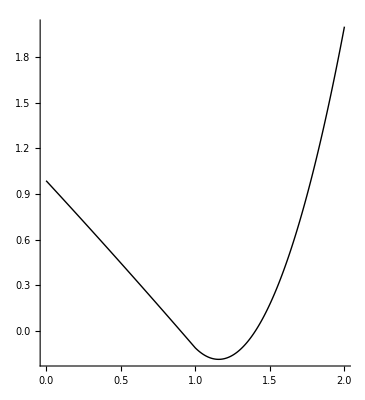

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```